Notebook for computing ⟨HES(N_1) | T | HES( N_2)⟩ for particular |HES⟩ microstates . 
All the kinematic variables are defines for the kinematics considered in  arXiv:2312.02127.

Instructions:

Set the values for N1, N2 and flag under “Inputs”. Choose the HES microstate partition through k1 and l1.

Once done, evaluate the initialization cells (Evaluation>>Evaluate Initialization Cells).

Run the cell following the subsection “HHT matrix computation”. Data is saved in the files “name1” (for peak positions), “name2” (for peak amplitudes), “name3” (for peak level spacings). See under “Initialized cells”.

In all three files, data is saved in the format:
 {{values for partition 1 of N1 and partition 1 of N2}, {values for partition 1 of N1 and partition 2 of N2},...,{values for partition 2 of N1 and partition 1 of N2},...,{values for last partition of N1 and last partition of N2}}.

To extract the generated data, use the command ReadList[filename]. Use “name1”,”name2”,”name3” in place of filename.

By default, the data files will be saved in the Home directory. To change the file location, uncomment the cell under “Directory” and use SetDirectory[“file-location”]. Put the desired file path in place of “file-location”.

```mathematica
Quit[];
```

## Directory:

```mathematica
(*SetDirectory["file-location"]*)
```

## Inputs:

Here, N1 ≡ N_1, N2≡N_2. For consistent kinematic choices, keep N1≥N2.

```mathematica
N1=22; N2=13;
```

For ζ_1.ζ_2=0, set: flag = 0
For ζ_1.ζ_2=1, set: flag = 1

```mathematica
flag=1;
```

k1 and l1 chooses the desired partition of N1 and N2. Thus k1 ≤ num1, k2 ≤ num2.

```mathematica
(* no. of partitions of N1 and N2 respectively *)
{num1,num2}
```

{num1,num2}

```mathematica
k1=RandomInteger[N1]; l1=RandomInteger[N2];
n1=part1[[k1]]
n2=part2[[l1]]
```

{17,3,1,1}

{13}

## Initialized cells

#### permutations, combinatorics:

```mathematica
Clear[permList,K12,rkList];

(* K12 = min(Subscript[J, 1],Subscript[J, 2]), here n1, n2 denote partitions *)
K12[n1_,n2_]:=Min[ Length[n1],Length[n2]];

(* generates all k-length subsets from a partition 'n' *)
rkList[n_,k_]:=Subsets[n,{k}]

(* generates all the permutations of the j-th element of the k-length subset list of the partition 'n1' *)
permList[n1_,k_,j_]:=Module[{list0,replace0,list1,a},
list0=rkList[n1,k][[j]](*j*);
replace0=Flatten[Table[{Subscript[a, i]->list0[[i]]},{i,1,Length[list0]} ]];
list1=Permutations[Table[Subscript[a, i],{i,1,Length[list0]}]]/.replace0;
list1]
```

```mathematica
part1=IntegerPartitions[N1];
part2=IntegerPartitions[N2];
num1=PartitionsP[N1];
num2=PartitionsP[N2];
```

#### kinematic factors:

```mathematica
(* γ , here y=Cos[χ] *)
Clear[γv];
γv[y_]:= (2 (-1+N1))/(-1+N1+N2-√(-3+N1 (2+N1)+2 N2-2 N1 N2+N2^2) y);
```

```mathematica
(* Subscript[ζ, 1].Subscript[p, 2] *)
Clear[ζ1p2];
ζ1p2[y_]:=-1/(2 √(-1+N1))√(-3+N1 (2+N1)+2 N2-2 N1 N2+N2^2) √(1-(2-2 N1+(-1+N1+N2) γv[y])^2/((-3+N1 (2+N1)+2 N2-2 N1 N2+N2^2) γv[y]^2))
```

```mathematica
(* Subscript[ζ, 2].Subscript[p, 1] *)
Clear[ζ2p1];
ζ2p1[y_]:=-1/(2 √(-1+N1))√(-3+N1 (2+N1)+2 N2-2 N1 N2+N2^2) γv[y] √(1-(2-2 N1+(-1+N1+N2) γv[y])^2/((-3+N1 (2+N1)+2 N2-2 N1 N2+N2^2) γv[y]^2))
```

#### amplitude components:

```mathematica
Clear[p,q1,q2];
p[r1_,r2_,y_]:= (-1)^r1 Product[((r1/γv[y]-r1+i)/i),{i,1,r1-1}]Product[((r2 γv[y]-r2+j)/j),{j,1,r2-1}](((γv[y]-1)r1 r2)/(r1-r2 γv[y]));
q1[r1_,y_]:=ζ1p2[y] (-1)^r1 Product[((r1/γv[y]-r1+i)/i),{i,1,r1-1}];
q2[r2_,y_]:=ζ2p1[y] Product[((r2 γv[y]-r2+j)/j),{j,1,r2-1}]
```

```mathematica
Clear[ampPart1];
ampPart1[n1_,n2_,i_,j_,k_]:=Module[{list01,list02},
list01=permList[n1,k,i];
list02=rkList[n2,k][[j]];
Sum[Product[(p[list01[[j1]][[x1]],list02[[x1]],y]),{x1,1,k}],{j1,Length[list01]}]
]
```

```mathematica
Clear[ampPart2];
ampPart2[n1_,n2_,i_,j_,k_]:=Module[{list03,list04},
list03=allList1[[Length[allList1]-(i+Sum[Binomial[Length[n1],m],{m,1,k-1}])]];
list04=allList2[[Length[allList2]-(j+Sum[Binomial[Length[n2],m],{m,1,k-1}])]];
Product[q1[s1,y],{s1,list03}]Product[q2[s2,y],{s2,list04}]
]
```

## Evaluation of HHT amplitude:

#### HHT matrix computation:

```mathematica
n1=part1[[k1]];
n2=part2[[l1]];
allList1=Subsets[n1];
allList2=Subsets[n2];
tempStore={};

(* tempStore contains the expression of the HHT amplitude for two partitions n1 and n2 *)
If[flag==0,

tempStore= Product[q1[s1,y],{s1,n1}]Product[q2[s2,y],{s2,n2}];,

tempStore= ParallelSum[Sum[ampPart1[n1,n2,i,j,k]ampPart2[n1,n2,i,j,k],{i,1,Length[rkList[n1,k]]},{j,1,Length[rkList[n2,k]]}],{k,1,K12[n1,n2]}]+ Product[q1[s1,y],{s1,n1}]Product[q2[s2,y],{s2,n2}]];




(* χ grid spacings *)
dX=0.001;
(* tempTab contains the numerical HHT amplitudes at χ grid points, x denotes χ *)
tempTab=Table[{x,tempStore/.{y -> Cos[x]}},{x,dX,π,dX}];
```

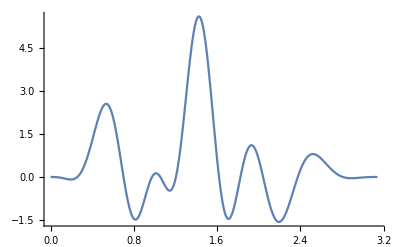

```mathematica
(* plot of the analytical expression *)
Plot[tempStore/.{y -> Cos[x]},{x,0,π},PlotRange->All]
```

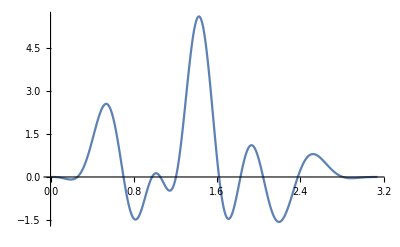

```mathematica
(* plot of the numerical expression *)
ListPlot[tempTab, Joined->True]
```